# Clase #1: Métodos numéricos- Mathematica

## operaciones básicas

```mathematica
3+5
```

8

```mathematica
3 4(*el espacio es multiplicación*)
```

12

```mathematica
N[4000/3,12]
```

1333.33333333

```mathematica
N[ⅇ^2,100]
```

7.389056098930650227230427460575007813180315570551847324087127822522573796079057763384312485079121795

```mathematica
N[π,273]
```

3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211706798214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196442881097566593344612847564823378678316527120190914564856692346034861045

```mathematica
Log[ⅇ^5]
```

5

```mathematica
N[Sin[90°]]
```

```mathematica
N[Cos[π/4]]
```

0.707107

```mathematica
Cos[π/4]
```

1/(√2)

## Operadores

```mathematica
Expand[(x+2)^3(x-1)^2]
```

x^5+4 x^4+x^3-10 x^2-4 x+8

```mathematica
Factor[x^2+2x+1]
```

(x+1)^2

```mathematica
Apart[(3x+2)/(x^3(x^2-1)(x^2+1))]
```

-2/x^3+(3-2 x)/(2 (x^2+1))-3/x^2+5/(4 (x-1))-1/(4 (x+1))

```mathematica
$PrePrint= TraditionalForm
```

TraditionalForm

```mathematica
D[3 x^3-5x ⅇ^(x^2),x]
```

-10 ⅇ^(x^2) x^2+9 x^2-5 ⅇ^(x^2)

```mathematica
FullSimplify[D[x y Sin[(ⅇ^(x z^3))/Log[z^2 Cos [x/z]]],z]]
```

(x y ⅇ^(x z^3) cos((ⅇ^(x z^3))/(log(z^2 cos(x/z)))) (3 x z^4 log(z^2 cos(x/z))-x tan(x/z)-2 z))/(z^2 log^2(z^2 cos(x/z)))

```mathematica
FullSimplify[D[x y Sin[(ⅇ^(x z^3))/Log[z^2 Cos [x/z]]],{z,2}]]
```

-1/(z^4 log^4(z^2 cos(x/z)))x y ⅇ^(x z^3) (ⅇ^(x z^3) sin((ⅇ^(x z^3))/(log(z^2 cos(x/z)))) (-3 x z^4 log(z^2 cos(x/z))+x tan(x/z)+2 z)^2-cos((ⅇ^(x z^3))/(log(z^2 cos(x/z)))) log(z^2 cos(x/z)) (log(z^2 cos(x/z)) (x^2-12 x z^5+3 x z^5 (3 x z^3+2) log(z^2 cos(x/z))+2 z^2)+x tan(x/z) (x tan(x/z) (log(z^2 cos(x/z))+2)+2 z ((1-3 x z^3) log(z^2 cos(x/z))+4))+8 z^2))

```mathematica
∫Sin[3x]ⅆx(*esc+intt+esc*)
```

-1/3 cos(3 x)

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π erf(x)

```mathematica
N[∫_0^∞ ⅇ^(-x^2)ⅆx,10]
```

0.8862269255

```mathematica
∫(3x+2)/(x^3(x^2-1)(x^2+1))ⅆx (*todo lo anterior con fracciones parciales*)
```

1/x^2-1/2 log(x^2+1)+3/x+5/4 log(1-x)-1/4 log(x+1)+3/2 tan^-1(x)

```mathematica
□
```

## Gráficas

### 2D

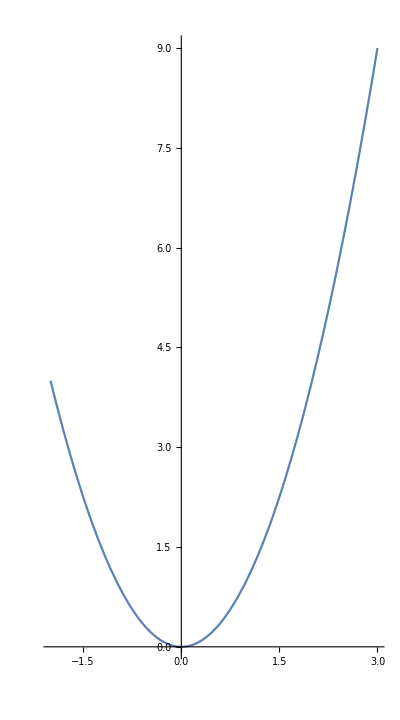

```mathematica
Plot[x^2, {x, -2,3},AspectRatio->9/5]
```

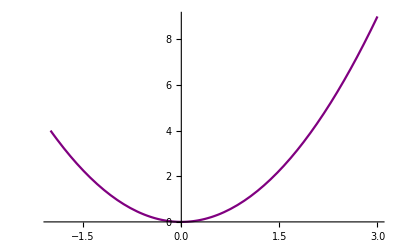

```mathematica
Plot[x^2, {x, -2,3},PlotStyle->Purple]
```

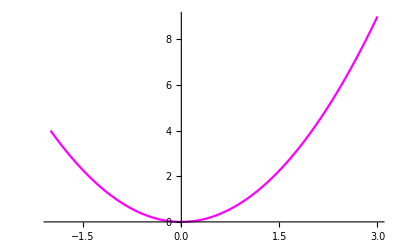

```mathematica
Plot[x^2, {x, -2,3},PlotStyle->RGBColor[1,0,1]]
```

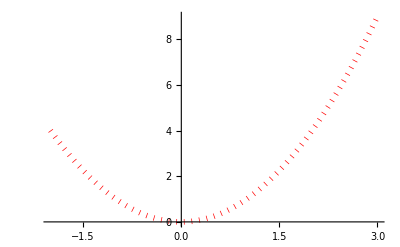

```mathematica
Plot[x^2, {x, -2,3},PlotStyle->Directive[Thickness[.01],Red, Dotted]]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotLabels->"Expressions", PlotStyle->Thick,ColorFunction->Function[{x,y},Hue[y]]]
```

-Graphics-

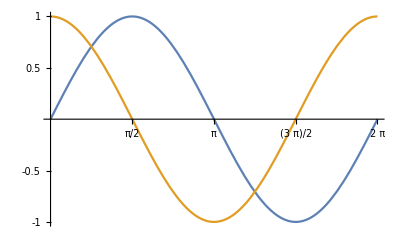

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}, Ticks->{{π/2,π,3/2 π,2π},{-1,-.5,.5,1}}]
```

```mathematica
Range[2,5]
```

{2,3,4,5}

```mathematica
Range[2,10,0.5]
```

{2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

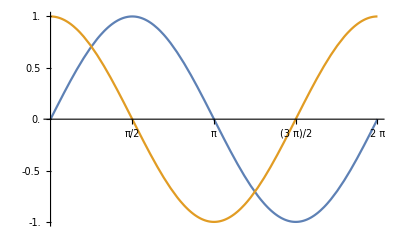

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}, Ticks->{{π/2,π,3/2 π,2π},Range[-1,1,0.5]}]
```

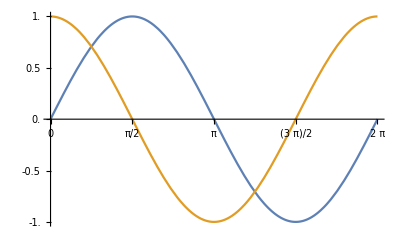

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}, Ticks->{Range[0,2π,π/8],Range[-1,1,0.5]}]
```

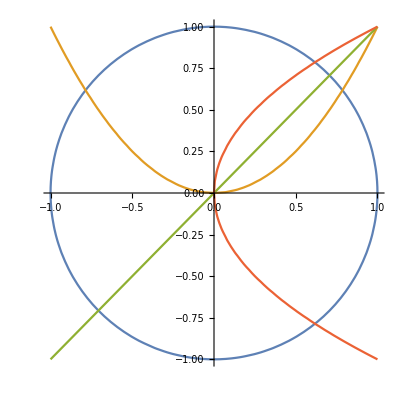

```mathematica
ContourPlot[{x^2+y^2==1,y==x^2,y==x, x==y^2}, {x, -1, 1},{y,-1,1},Frame->False,Axes-> True]
```

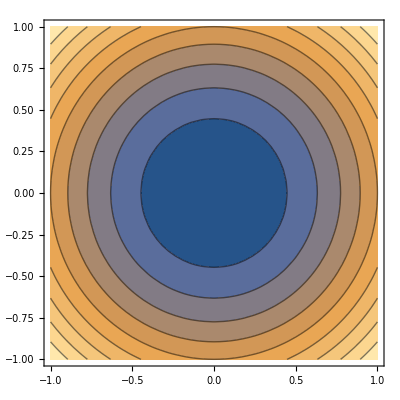

```mathematica
ContourPlot[x^2+y^2,{x, -1,1}, {y,-1,1}](*curvas de nivel*)
```

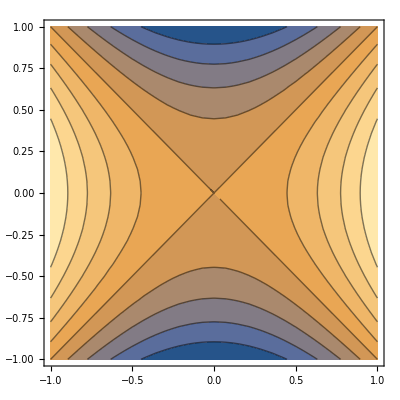

```mathematica
ContourPlot[x^2-y^2,{x, -1,1}, {y,-1,1}](*curvas de nivel: la silla*)
```



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}]
```

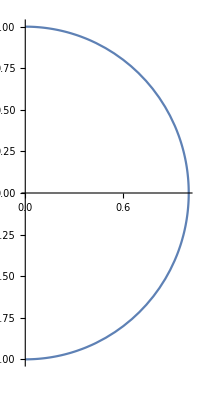

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,π}](*empieza desde el eje y y dibuja en sentido de las manecillas de l reloj*)
```

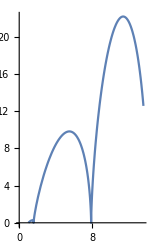

```mathematica
ParametricPlot[{Cos[t]+1t,t-t Sin[t]}, {t,0,4π}]
```

```mathematica
(*movimiento de la luna en vista al sol*)ParametricPlot[{5Cos[t]+Cos[12t],5Sin[t]+sin[12t]},{t,0,2π}]
```

-Graphics-

### 3D

```mathematica
Plot3D[x^2+y^2, {x,-2,2},{y,-2,2} ]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,x^2-y^2}, {x,-2,2},{y,-2,2} ]
```

-Graphics3D-

```mathematica
Plot3D[√(1-x^2-y^2),{x,-2,2},{y,-2,2},Boxed->False,AxesOrigin->{0,0,0},PlotStyle->Opacity[0.6]]
```

-Graphics3D-

```mathematica
ContourPlot3D[z==x^2+y^2,{x,-2,2},{y,-2,2},{z,0,4}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2/4+y^2/9+z^2==1,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

## variables y funciones

```mathematica
a=45(*que no salgan valores de salida poner ;*)
```

45

```mathematica
Clear [a](*con esto borra el valor de la variable*)
```

```mathematica
b=Sin[x]
```

Sin[x]



```mathematica
Plot[b,{x,0,2π}]
```

```mathematica
Sin[a °]
```

```mathematica
Sin[a °]
```

Sin[a °]

```mathematica
lista=Range[0,2π,π/8];
```

```mathematica
N[Sin[lista]]
```

{0.,0.382683,0.707107,0.92388,1.,0.92388,0.707107,0.382683,0.,-0.382683,-0.707107,-0.92388,-1.,-0.92388,-0.707107,-0.382683,0.}

```mathematica
func=3 x^3+2x-5;
```

```mathematica
func/.x->{0,2,3}
```

{-5,23,82}

```mathematica
func/.x->Range[0,10,1]
```

{-5,0,23,82,195,380,655,1038,1547,2200,3015}

```mathematica
Solve[a1 x +b1 ==c, x](*despeja x*)
```

{{x→(-b1+c)/a1}}

```mathematica
Clear[a,b]
```

```mathematica
Solve[a x^2+b x +c ==0,x](*la chicharronera*)
```

{{x→(-√(b^2-4 a c)-b)/(2 a)},{x→(√(b^2-4 a c)-b)/(2 a)}}

```mathematica
$PrePrint=TraditionalForm
```

TraditionalForm

```mathematica
Solve[a x^3+b x^2 +c x +d==0,x](*la imposible*)
```

{{x→((√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))/(3 2^(1/3) a)-(2^(1/3) (3 a c-b^2))/(3 a (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))-b/(3 a)},{x→-((1-ⅈ √3) (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))/(6 2^(1/3) a)+((1+ⅈ √3) (3 a c-b^2))/(3 2^(2/3) a (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))-b/(3 a)},{x→-((1+ⅈ √3) (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))/(6 2^(1/3) a)+((1-ⅈ √3) (3 a c-b^2))/(3 2^(2/3) a (√((-27 a^2 d+9 a b c-2 b^3)^2+4 (3 a c-b^2)^3)-27 a^2 d+9 a b c-2 b^3)^(1/3))-b/(3 a)}}

```mathematica
a = NSolve[x^2+5 x +6 ==0 ,x]
```

{{x→-3.},{x→-2.}}

```mathematica
a = NSolve[x^3+5 x^2 +23 x +2==0 ,x,Reals]
```

{{x→-0.0886341}}

```mathematica
func /. a
```

{-92,-33}

```mathematica
D[x^4-12 x^2+x-1]
```

x^4-12 x^2+x-1

```mathematica
D[3 x^3-5x ⅇ^(x^2),x]
```

-10 ⅇ^(x^2) x^2+9 x^2-5 ⅇ^(x^2)

```mathematica
D[x^4-12 x^2+x-1,x]
```

4 x^3-24 x+1

```mathematica
Solve[4 x^3-24x+1 ==0,x]
```

{{x→4/(-1+ⅈ √511)^(1/3)+1/2 (-1+ⅈ √511)^(1/3)},{x→-(2 (1+ⅈ √3))/(-1+ⅈ √511)^(1/3)-1/4 (1-ⅈ √3) (-1+ⅈ √511)^(1/3)},{x→-(2 (1-ⅈ √3))/(-1+ⅈ √511)^(1/3)-1/4 (1+ⅈ √3) (-1+ⅈ √511)^(1/3)}}

```mathematica
clear[a]
```

clear({{x→-0.0886341}})

```mathematica
a=NSolve[4 x^3-24x+1 ==0,x]
```

{{x→-2.47006},{x→0.0416787},{x→2.42838}}

```mathematica
D[4 x^3-24x+1,x]
```

12 x^2-24

```mathematica
D[4 x^3-24x+1, x]
```

12 x^2-24

```mathematica
func /. a(*esta mal. corregirlo*)
```

{-55.1513,-4.91643,42.8177}

```mathematica
f=x^4-12 x^2+x-1;
```

```mathematica
d1=D[f,x];
```

```mathematica
sol=NSolve[D[f,x]==0,x];
d2=D[d1,x];
d2/.sol
```

{49.2145,-23.9792,46.7646}

```mathematica
(*Otra forma resuelta del profe*)
f=x^4-12 x^2+x-1;
D[f,{x,2}]/NSolve[D[f,x]==0,x]
```

((12 x^2-24)/(x→-2.47006)
(12 x^2-24)/(x→0.0416787)
(12 x^2-24)/(x→2.42838))

```mathematica
clear[funcder]
```

```mathematica
clear[-1+x-12 x^2+x^4](*este no cuenta*)
funcder = x^4-12 x^2+x-1; (*se pone la funcion original*)
derivate1 = D[funcder,x]; (*se face una variable llamada derivate1 ue su funcio es derivar la funcion original*)
solmio = NSolve[D[funcder,x]==0,x]; (*la funcion solmio es para la resolución de la ecuación igualando a 0 del resultado de la derivada de la funcion original*)
derivate2= D[derivate1,x]; (*se crea otra variable derivate 2 que deriva derivate 1 *)
derivate2/.solmio (*se evalua la derivada con la resolución de los puntos dados en solmio*)
```

clear[-1+x-12 x^2+x^4]

{49.2145,-23.9792,46.7646}

```mathematica
clear[f]
```

clear[f]

```mathematica
(*Primer problema de maximos y minimos*)
f=-x^2(x-2)^2;
d1=D[f,x];
sol=NSolve[D[f,x]==0,x];
d2=D[f, {x,2}];
d2/.sol
```

{-8.,4.,-8.}

## Programación básica

### Halla el número mayor

```mathematica
a= 2;b=10;
If[(*cond*)a>b,(*verdadero*) Print["El es mayor es: ", a], (*falso*)
Print["El mayor es: ",b]]
```

El mayor es: 10

```mathematica
(*plantilla*)
mayor[a_,b_]:=Module[{(*variales internas*)},
If[(*cond*)a>b,(*verdadero*) Print["El es mayor es: ", a], (*falso*)
Print["El mayor es: ",b]]
(*el cuerpo del programa*)]
```

```mathematica
mayor[12,89](*aquí es el exe del programa*)(*le metemos los valos a comprar*)
```

El mayor es: 89

```mathematica
mayor[100,2]
```

El es mayor es: 100

```mathematica
mayor[32,12]
```

El es mayor es: 32

### Hallar máximos y mínimos

```mathematica
(*programa para máximos y mínimos*)
(*Primer problema de maximos y minimos con derivada*)
maxmin[f_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0,x];
d2=D[f, {x,2}];
d2/.sol;
seg = d2/.sol;
If[seg[[1]]>0, Print["Minimo en"],sol [[1]]] Print["Maximo en",sol[[1]]];
If[seg[[2]]>0, Print["Minimo en"],sol [[2]]] Print["Maximo en",sol[[2]]];
If[seg[[3]]>0, Print["Minimo en"],sol [[3]]] Print["Maximo en",sol[[3]]];
]
```

```mathematica
maxmin[f=-x^2(x-2)^2 ]
```

Maximo en{x→0.}

Minimo en

Maximo en{x→1.}

Maximo en{x→2.}

```mathematica
Range[6]
```

{1,2,3,4,5,6}

```mathematica
Range[2,7]
```

{2,3,4,5,6,7}

```mathematica
Table[(*cuerpo del programa*)"Fernando",(*índices*){i,6,9}]
```

{Fernando,Fernando,Fernando,Fernando}

```mathematica
Table[(*cuerpo del programa*)Print["Fernando"],(*índices*){i,6,9}];
```

Fernando

Fernando

Fernando

«1 more identical outputs»

```mathematica
Table[3i + 1,{i,3,7}]
```

{10,13,16,19,22}

```mathematica
lis=Table[3i + 1,{i,3,7}];
```

```mathematica
lis
```

{10,13,16,19,22}

```mathematica
Length[lis]
```

5

```mathematica
lis2={{2,3},{5,6},{-1,56}}
```

(2 | 3
5 | 6
-1 | 56)

```mathematica
$PrePrint= TraditionalForm
```

TraditionalForm

```mathematica
lis2[[2,1]]
```

```mathematica
5
```

```mathematica
(*numero de renglones*)
Length[lis2]
```

3

```mathematica
(*forma de saber el numero de columnas*)
Length[lis2]
```

3

```mathematica
lis=Table[{3i+1},{i,3,7}]
```

(10
13
16
19
22)

```mathematica
{Table[3i+1,{i,3,7}]}
```

(10 | 13 | 16 | 19 | 22)

```mathematica
(*programa para máximos y mínimos*)
(*Primer problema de maximos y minimos con derivada*)
maxmin[f_]:=Module[{},d1=D[f,x];
sol=NSolve[D[f,x]==0,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;
(*Impresion de valores con tabla, basandonos en la solución de máximos y mínimos*)
(*en los valores de la tabla se introduce el índice, en este caso con la letra i.*)
(*comando nuevo para quitar las flechas del resultado es con x/.(mas el nombre de los valores del máximo y mínimo )*)
Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
(*en la parte de {i,Lenght [sol] es para introducir la longitud de la tabla y no solo asignarle un número donde evaluar}*)
]
```

```mathematica
maxmin[f]
```

Maximo en =  0.

Minimo en x = 1.

Maximo en =  2.

```mathematica
x/.sol
```

{0.,1.,2.}

```mathematica
maxmin[f]
```

Maximo en =  0.

Minimo en x = 1.

Maximo en =  2.

```mathematica
f= x √(1-x^2); (*con el programa anterior cambiamos el valor de la funcion f*)
```

```mathematica
maxmin[f](*maximos y minimos de l nueva función *)
```

Maximo en =  0.707107

Minimo en x = -0.707107

```mathematica
(*programa para máximos y mínimos*)
(*Primer problema de los ejercicios que el profe dio*)
(*se le agrgan intervalos para evaluacion desde donde a donde a_,b_*)
(*ejercicio #10*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
(*==0 && a<x<b,x se iguala a 0 y se declaran los intervalos a los cuales de va a evaluar*)
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f=D[8 x^2+ 1/x,x];
```

Maximo en =  -0.5

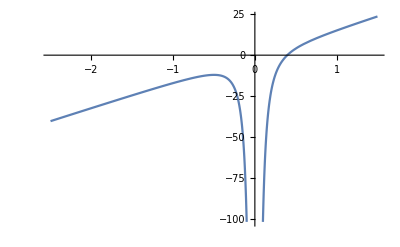

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
(*programa para máximos y mínimos*)
(*Primer problema de los ejercicios que el profe dio*)
(*se le agrgan intervalos para evaluacion desde donde a donde a_,b_*)
(*ejercicio #9*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
(*==0 && a<x<b,x se iguala a 0 y se declaran los intervalos a los cuales de va a evaluar*)
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f=D[x^3-4 x^2,x];
```

Minimo en x = 1.33333

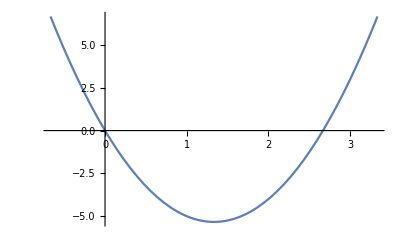

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
(*programa para máximos y mínimos*)
(*Primer problema de los ejercicios que el profe dio*)
(*se le agrgan intervalos para evaluacion desde donde a donde a_,b_*)
(*ejercicio #11(a)*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
(*==0 && a<x<b,x se iguala a 0 y se declaran los intervalos a los cuales de va a evaluar*)
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f=x(2-2/3 x);
```

Maximo en =  1.5

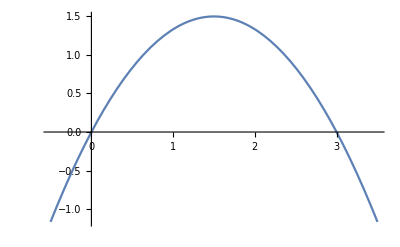

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
(*programa para máximos y mínimos*)
(*Primer problema de los ejercicios que el profe dio*)
(*se le agrgan intervalos para evaluacion desde donde a donde a_,b_*)
(*ejercicio #11(b)*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
(*==0 && a<x<b,x se iguala a 0 y se declaran los intervalos a los cuales de va a evaluar*)
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f=2x(24-x^2);
```

Minimo en x = -2.82843

Maximo en =  2.82843

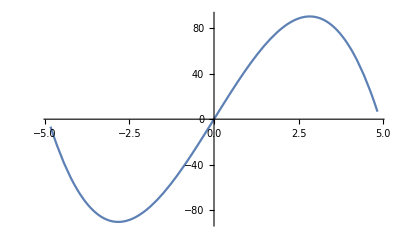

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
{2x/. sol[[2]], (24-x^2)/.sol[[2]]}
```

{5.65685,16.}